Approximation of turn-over of PRDM9 as a function of ε

## Third order approximation

```mathematica
ClearAll["Global`*"]
```

### Third order approximation of Mimimun activity (Linf) as a function of L

```mathematica
SX = x /.Solve[L(x-x^2/2+x^3/3)==x, x]
```

{0,(3 L-√3 √(16 L-13 L^2))/(4 L),(3 L+√3 √(16 L-13 L^2))/(4 L)}

```mathematica
Linf= FullSimplify[1+SX[[2]]]
```

7/4-(√(48-39 L))/(4 √L)

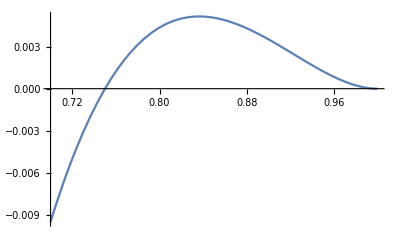

```mathematica
Plot[1- 2 *L +Linf,{L,0.7,1}]
```

### Solving mean activity (L) as a function of ε

```mathematica
Solve[(1-L) (1-Linf)/ (L^2) == eps,L]
```

{{L→Root[-6+18 #1-18 #1^2+(6+3 eps) #1^3-3 eps #1^4+2 eps^2 #1^5&,1]},{L→Root[-6+18 #1-18 #1^2+(6+3 eps) #1^3-3 eps #1^4+2 eps^2 #1^5&,2]},{L→Root[-6+18 #1-18 #1^2+(6+3 eps) #1^3-3 eps #1^4+2 eps^2 #1^5&,3]},{L→Root[-6+18 #1-18 #1^2+(6+3 eps) #1^3-3 eps #1^4+2 eps^2 #1^5&,4]},{L→Root[-6+18 #1-18 #1^2+(6+3 eps) #1^3-3 eps #1^4+2 eps^2 #1^5&,5]}}

### Approximation of mean activity (L) as a function of ε

```mathematica
serie= Series[(1-L) (1-Linf)/ (L^2),{L,1,3}]
```

2 (L-1)^2-10/3 (L-1)^3+O[L-1]^4

```mathematica
SL = L/. Solve[Normal[serie ]== eps,L]
```

{1/5 (6-2^(2/3)/((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))-((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))/2^(2/3)),6/5+(1+ⅈ √3)/(5 2^(1/3) (-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))+((1-ⅈ √3) (-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))/(10 2^(2/3)),6/5+(1-ⅈ √3)/(5 2^(1/3) (-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))+((1+ⅈ √3) (-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))/(10 2^(2/3))}

```mathematica
L= SL[[1]]
```

1/5 (6-2^(2/3)/((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))-((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))/2^(2/3))

### PRDM9 diversity (Ke) as a function of ε

#### rho = Ne * v * r_ 0 * \alpha

```mathematica
K = rho * L /(1- 2 *L +Linf)
```

((6-2^(2/3)/((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))-((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))/2^(2/3)) rho)/(5 (11/4-2/5 (6-2^(2/3)/((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))-((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))/2^(2/3))-(√5 √(48-39/5 (6-2^(2/3)/((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))-((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))/2^(2/3))))/(4 √(6-2^(2/3)/((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))-((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))/2^(2/3)))))

```mathematica
T = K / (u* N* alpha*(1- L)/L)
```

((6-2^(2/3)/((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))-((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))/2^(2/3))^2 rho)/(25 alpha (1+1/5 (-6+2^(2/3)/((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))+((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))/2^(2/3))) (11/4-2/5 (6-2^(2/3)/((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))-((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))/2^(2/3))-(√5 √(48-39/5 (6-2^(2/3)/((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))-((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))/2^(2/3))))/(4 √(6-2^(2/3)/((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))-((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))/2^(2/3)))) N u)

```mathematica
FullSimplify[Series[T,{eps,0,1}]]
```

Series::ztest: Unable to decide whether numeric quantities {√(2/3) ⅇ^((ⅈ π)/6)-√(2/3) ⅇ^((5 ⅈ π)/6)-(25 ⅇ^((ⅈ π)/6))/(√(1/2 (2+13 Power[«2»]-13 Power[«2»])) (6-ⅇ^(Times«1»«1»])+ⅇ^((«1»)/3))^(3/2))+(25 ⅇ^((5 ⅈ π)/6))/(√(1/2 (2+13 Power[«2»]-13 Power[«2»])) (6-ⅇ^Times[«2»]+ⅇ^((2 ⅈ π)/3))^(3/2)),«1»,√(2/3) ⅇ^((ⅈ π)/6)-√(2/3) ⅇ^((5 «1»«1»π)/6)+(25 «1» √(2 «1»))/((«1»)^(«1») «1»)-(25 ⅇ^((«1»)/6) √(2 (2+13 Power[«2»]-13 Power[«2»])))/((6-ⅇ^(«1»)+ⅇ^((«1»)/3))^(3/2) (-2-13 ⅇ^(Times«1»«1»])+13 ⅇ^Times[«2»]))} are equal to zero. Assuming they are.

(3 √2 rho)/(alpha N u eps^(3/2))+(37 rho)/(2 alpha N u eps)+(343 rho)/(8 √2 alpha N u √eps)+(2843 rho)/(36 alpha N u)+(1747015 rho √eps)/(6912 √2 alpha N u)+(36814 rho eps)/(81 alpha N u)+(17095949 rho eps^(3/2))/(12288 √2 alpha N u)+O[eps]^2